```mathematica
Метод обратной функции
```

```mathematica
Clear[callx,initx,genx]
Integrate[(1-μ^2)/2/(1+μ^2-2μ x)^(3/2),{x,-1,1},Assumptions->{μ>-1&&μ<1}]
```

1

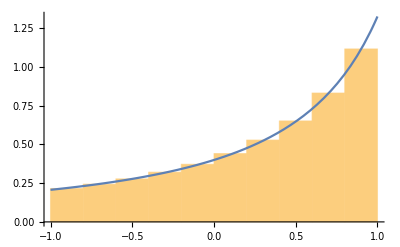

```mathematica
a=ProbabilityDistribution[(1-μ^2)/2/(1+μ^2-2μ x)^(3/2),{x,-1,1}];
initx[prg_,μ1_]:=(
μ[prg]^=μ1;
s[prg] ^=NSolve[Rationalize[(CDF[a/.μ->μ1]@x)]==r,x,Reals]//First;
);
callx[prg_]:=(
x/.s[prg]/. r->RandomReal[]
)
initx[genx,0.3]
Show[{Histogram[Table[callx[genx],{100000}],10,PDF],Plot[PDF[a/.μ->0.3][x],{x,-1,1}]}]
```

```mathematica
Конструирование двумерного моделируемого вектора с зависимыми координатами
```

```mathematica
Clear[callu,initu,genu,callv,initv,genv]
b=ProbabilityDistribution[Integrate[3(u^2)(u+1)(v^u)Exp[-u^3],{v,0,1},Assumptions->{u>0}],{u,0,Infinity}];
initu[prg1_]:=(
s[prg1] ^=Solve[(CDF[b,u])==r,u,Reals]//First;
);
callu[prg1_]:=(
u/.s[prg1]/. r->RandomReal[]
)
c=ProbabilityDistribution[3(u^2)(u+1)(v^u)Exp[-u^3]/Integrate[3(u^2)(u+1)(v^u)Exp[-u^3],{v,0,1},Assumptions->{u>0}],{v,0,1}];
initv[prg2_]:=(
s1[prg2] ^=Assuming[{u>0 ,v>0,v<1},Solve[CDF[c,v]==r,v]]//First;
);
callv[prg2_,u2_]:=(
v/.s1[prg2]/. r->RandomReal[]/.u->u2
)
initu[genu]
initv[genv]
hist=Histogram3D[Table[With[{ut=callu[genu]},{callv[genv,ut],ut}],{10000}],Automatic,PDF];
Show[hist,Plot3D[3u^2(u+1)v^u Exp[-u^3],{v,0,1},{u,0,2}]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-Graphics3D-

```mathematica
Метод дискретной суперпозиции
```

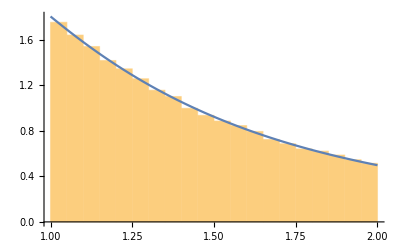

```mathematica
Clear[calls,inits,gens,f,p1,p2,distr1,distr2]
p1=Integrate[5u/(1+u^2)^2,{u,1,2}];
p2=Integrate[Sqrt[2]π Sin[π/(2u)]/(8 u^2),{u,1,2}];
f=5u/((1+u^2)^2)+(Sqrt[2]π/8/u^2)Sin[π/2/u];
distr=ProbabilityDistribution[f/(p1+p2),{u,1,2}];
distr1=ProbabilityDistribution[5u/(1+u^2)^2/p1,{u,1,2}];
distr2=ProbabilityDistribution[Sqrt[2]π Sin[π/(2u)]/(8 u^2)/p2,{u,1,2}];
inits[prg3_]:=(
s1[prg3] ^=NSolve[(CDF[distr1,u])==r,u,Reals]//First;
s2[prg3] ^=NSolve[(CDF[distr2,u])==r,u,Reals]//First;
)
calls[prg3_]:=(
With[{rr=RandomReal[]},If[rr<p1,u/.s1[prg3]/.r->RandomReal[],u/.s2[prg3]/.r->RandomReal[]]]
)
inits[gens]
Show[{Histogram[Table[calls[gens],{100000}],Automatic,PDF],Plot[f,{u,1,2}]}]
```

```mathematica
Метод исключения
```

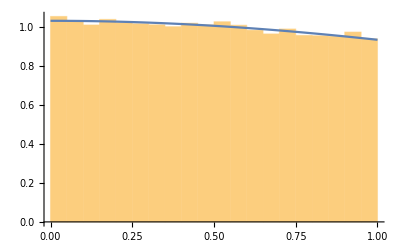

```mathematica
clear[distrM,genm,u,initm,init,f];
f[x_]:=1/((x^2)Log10[x+10]+10)
pM=Integrate[1/(u^2+10),{u,0,1}];
distrM:=ProbabilityDistribution[1/(u^2+10)/pM,{u,0,1}];
initm[prg4_]:=(
s[prg4] ^=NSolve[(CDF[distrM,u])==r,u,Reals]//First;
)
callm[prg4_]:=(
u/.s[prg4]/. r->RandomReal[]
)
initm[genm]
callf[prg5_]:=(
x0=callm[prg5];
y0=RandomReal[]/(x0^2+10);
While[y0>f[x0],
x0=callm[prg5];
y0=RandomReal[]/(x0^2+10);];
x0
)
G=NIntegrate[1/(u^2Log10[u+10]+10),{u,0,1}];
Show[{Histogram[Table[callf[genm],{100000}],Automatic,PDF],Plot[f[x]/G,{x,0,1}]}]
```

```mathematica
intG[n_]:=Total[Table[f[callf[genm]],{n}]/n];
G
intG[10000]
intGErr[n0_]:=(
x=Table[f[callf[genm]],{n0}];
Sqrt[(Total[(x^2)/n0]-Total[x/n0]^2)]     (*наверное я неправильно дисперсию написал*)
)
intGErr[10]
intGErr[100]
intGErr[1000]
intGErr[10000]
```

0.0967616

0.0968983

0.00190533

0.00258963

0.00276215

0.00283656

```mathematica
Выборка по важности
```

```mathematica
genn:=InverseCDF[NormalDistribution[0,1],RandomReal[]];
int[n_]:=Total[Table[With[{x1=genn,x2=genn,x3=genn,x4=genn},Sqrt[1+((Sin[x1 x2 x3 x4])^3)/12]],{n}]]/n
int[100000]
interr[n_]:=With[{l=Table[With[{x1=genn,x2=genn,x3=genn,x4=genn},Sqrt[1+((Sin[x1 x2 x3 x4])^3)/12]],{n}]},(Total[l^2]/n-Total[l]^2/n^2)]
interr[10000]
NIntegrate[Exp[-(x1^2+x2^2+x3^2+x4^2)/2]Sqrt[1+(Sin[x1 x2 x3 x4])^3/12],{x1,-∞,∞},{x2,-∞,∞},{x3,-∞,∞},{x4,-∞,∞}]/(2π)^2
NIntegrate[Exp[-(x1^2+x2^2+x3^2+x4^2)/2]Sqrt[1+(Sin[x1 x2 x3 x4])^3/12],{x1,-∞,∞},{x2,-∞,∞},{x3,-∞,∞},{x4,-∞,∞},Method->"GlobalAdaptive"]/(2π)^2
NIntegrate[Exp[-(x1^2+x2^2+x3^2+x4^2)/2]Sqrt[1+(Sin[x1 x2 x3 x4])^3/12],{x1,-∞,∞},{x2,-∞,∞},{x3,-∞,∞},{x4,-∞,∞},Method->"MonteCarlo"]/(2π)^2
```

1.00001

0.000114616

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 39.4764 and 0.00712146 for the integral and error estimates.

0.999948

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 39.4764 and 0.00712146 for the integral and error estimates.

0.999948

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 38.6693 and 1.0452 for the integral and error estimates.

0.979504